```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads,LEFT]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[Join[RandomSample[Join[s[13,36,13,36]],concentration],RandomSample[Join[s[1,12,1,50],s[37,50,1,50],s[13,36,1,12],s[13,36,37,50]],50-concentration]],First],10000]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,41,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;50,1;;50]]=LEFT[ω,50];MAT]
```

```mathematica
SLLEAD[1,50]
```

{{0.377737-0.668031 ⅈ,-0.313795-0.33669 ⅈ,-0.168606+0.144729 ⅈ,0.0927188+0.0515653 ⅈ,43,-0.000250297+0.000238966 ⅈ,0.00350276+0.0034116 ⅈ,-0.00337334-0.00352572 ⅈ},{1},46,{1},{1}}
 |  |  |  |

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[41;;50,41;;50]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=50},Inverse[IdentityMatrix[50]-g[ω,0.0001,-1,0].T[1,50].SLLEAD[ω,50].T[1,50]].g[ω,0.0001,-1,0]]
```

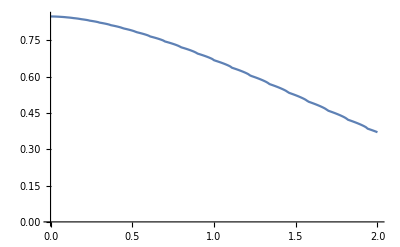

```mathematica
ListLinePlot[Table[{ω,-Im[device1[ω][[50,50]]]},{ω,Range[0,2,0.01]}]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J1= SLLEAD[ω,50]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,50}];J]],{unitcell,50}];J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

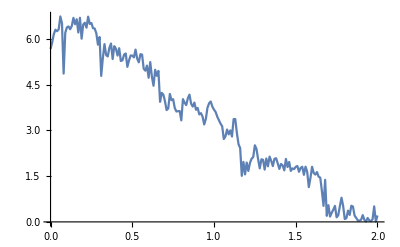

```mathematica
ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,0,50,1]},{ω,Range[0,2,0.01]}]]
```

```mathematica
Monitor[Table[Monitor[Table[Mean[ParallelTable[CA[ω,0.0001,1,0,1,conc,n],{n,800}]],{conc,5,45,5}],conc],{ω,Range[0,1,0.2]}],ω]
```

{{3.49138,3.21003,2.93981,2.76658,2.71704,2.56865,2.47645,2.37315,2.32301},{3.15917,2.95023,2.96848,2.8493,2.8197,2.75922,2.76977,2.639,2.68537},{3.05666,2.94108,2.93455,2.96519,2.85453,2.88889,2.83654,2.80276,2.81767},{3.04227,2.97376,2.97406,2.9313,2.90481,2.93521,2.93724,2.88606,2.89573},{2.75463,2.71484,2.69304,2.65808,2.68198,2.63318,2.67005,2.70026,2.69707},{3.13224,3.09232,3.09492,3.09599,3.06424,3.0545,3.06973,3.03415,3.0372}}

```mathematica
Manipulate[ListLinePlot[%24[[x]]],{x,Range[1,6,1]}]
```